```mathematica
Manipulate[StreamPlot[{a*(x[t]^n/(th^n + x[t]^n) )+ b * (th^n/(th^n + y[t]^n))- k*x[t],a*(y[t]^n/(th^n + y[t]^n) )+ b * (th^n/(th^n + x[t]^n)) - k*y[t]},{x[t],-15,15},{y[t],-15,15},StreamStyle->Black,FrameLabel->{Style["x = GATA1",15,Black],Style["y = PU.1",15,Black]},PlotLabel->Style["",18,Black]],{{a,0},0,2,Appearance->"Labeled"},{{b,1},0,2,Appearance->"Labeled"},{{k,0},-2,2,Appearance->"Labeled"},{{n,4},0,4,Appearance->"Labeled"},{{th,0.5},0,2,Appearance->"Labeled"}]
```

```mathematica
th=0.9;
k=1;
n=4;
a=1;
b=1;
```

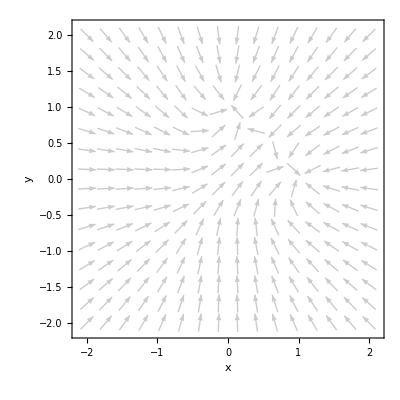

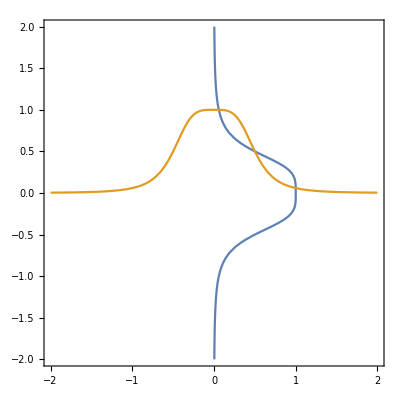

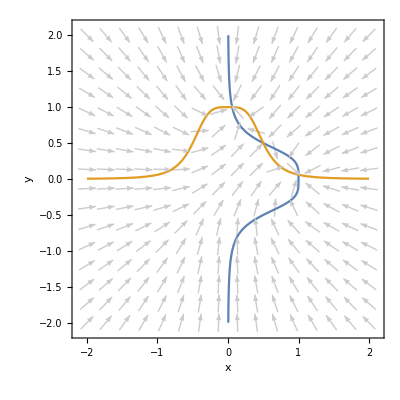

```mathematica
f[x_,y_]=a*(x^n/(th^n + x^n) )+ b * (th^n/(th^n + y^n))- k*x;
g[x_,y_]=a*(y^n/(th^n + y^n) )+ b * (th^n/(th^n + x^n)) - k*y;
vp=VectorPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}]
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-2,2},{y,-2,2}]
ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}];
Abs[{ptRules}];
Show[vp,cp,ptRules]
```